# Leapfrog approach (coupled transmission lines)

## Input Voltage

```mathematica
Vinp=0.04(*Volt*)
```

0.04

```mathematica
Winp=Vinp(*Volt*)
```

0.04

## Pore Resistance as Function of Input Voltage

```mathematica
(*From pore resistance simulation: 'nanoporemodel.np' notebook*)
```

```mathematica
RpData={{0.01,3.084034501333908*^15},{0.02,4.815156334595465*^15},{0.03,6.144893660866152*^15},{0.04,7.250037665050994*^15},{0.05,8.36066276728238*^15},{0.06,9.276964344063138*^15},{0.07,1.0069993000005158*^16},{0.08,1.0941273138122078*^16},{0.09,1.1763519144451374*^16},{0.1,1.254104407958279*^16}}
```

{{0.01,3.08403×10^15},{0.02,4.81516×10^15},{0.03,6.14489×10^15},{0.04,7.25004×10^15},{0.05,8.36066×10^15},{0.06,9.27696×10^15},{0.07,1.007×10^16},{0.08,1.09413×10^16},{0.09,1.17635×10^16},{0.1,1.2541×10^16}}

## MT Coupled Line Parameters

### common parameters

```mathematica
index=Vinp/0.01;
```

```mathematica
Rp =RpData[[index]][[2]](*Ω*)
```

7.25004×10^15

```mathematica
β=1.6*^-8(*m*);
```

### outer line

```mathematica
C10 =2.3033933765698123*^-16(*F*);(*From MT Poisson calculations: 'MT-poisson-solution-capacitance.nb' notebook*)
```

```mathematica
b1=0.06(*V^-1*);
```

```mathematica
Z1=1.8620411869695984*^11(*Ω*)
```

1.86204×10^11

```mathematica
Rl=5.845272415614076*^6(*Ω*)(*From MT Poisson calculations: 'MT-poisson-solution-plot-Resistances-Rl-rhol.nb' notebook*)
```

5.84527×10^6

```mathematica
Rt=7.791503282804299*^14(*Ω*)
```

7.7915×10^14

```mathematica
RtEquiv=(1/Rp+1/Rt)^-1
```

7.03542×10^14

```mathematica
γ1 = 3/(b1 √Z1)
```

0.000115871

### inner line parameters

```mathematica
C20 =1.356864332185853*^-16(*F*);(*From MT Poisson calculations: 'MT-poisson-solution-capacitance.nb' notebook*)
```

```mathematica
b2=0.03(*V^-1*)
```

0.03

```mathematica
ρl=1.8101102456764366*^7(*Ω*)(*From MT Poisson calculations: 'MT-poisson-solution-plot-Resistances-Rl-rhol.nb' notebook*)
```

1.81011×10^7

```mathematica
ρt=3.778537666038907*^14(*Ω*)
```

3.77854×10^14

```mathematica
ρtEquiv=(1/Rp+1/ρt)^-1(*Ω*)
```

3.59136×10^14

```mathematica
Z2 =3.1256404532992*^11(*Ω*)
```

3.12564×10^11

```mathematica
γ2 = 3/(b2 *√Z2)
```

0.000178867

### transformation parameter

```mathematica
α=√(C10*Z1*C20*Z2)(*sec*)
```

0.0000426497

### input amplitude κ_1 and κ_2 calculations

```mathematica
k1Not=√((12*Vinp)/(γ1 *√Z1))
```

0.0979796

```mathematica
k2Not=√((12*Winp)/(γ2 *√Z2))
```

0.069282

```mathematica
kk=Mean[{k1Not,k2Not}]
```

0.0836308

### coupled equations parameters

```mathematica
N1=24*(Z1/Rp*RtEquiv/Rt+Rl/Z1)*(√(C20*Z2))/(√(C10*Z1))(*equation S33*)
```

0.00130264

```mathematica
N2=24*RtEquiv/Rt*(√(Z1*Z2))/Rp*(√(C20*Z2))/(√(C10*Z1))*(1+(Rt*ρl)/(Z1*Z2))*γ2/γ1(*equation S34*)
```

0.00137516

```mathematica
N3=24*(Z2/Rp*ρtEquiv/ρt+ρl/Z2)*(√(C10*Z1))/(√(C20*Z2))(*equation S35*)
```

0.00238669

```mathematica
N4=24*ρtEquiv/ρt*(√(Z1*Z2))/Rp*(√(C10*Z1))/(√(C20*Z2))*(1+(ρt*Rl)/(Z1*Z2))*γ1/γ2(*equation S36*)
```

0.000513254

```mathematica
M1=24*(RtEquiv/Rt*(√(C20*Z2))/(√(C10*Z1))-1)(*equation S39*)
```

-2.45042

```mathematica
M2=24*ρt/Rp*RtEquiv/Rt*(C20*√Z2)/(C10*√Z1)*γ2/γ1(*equation S40*)
```

1.33064

```mathematica
M3=24*(ρtEquiv/ρt*(√(C10*Z1))/(√(C20*Z2))-1)(*equation S41*)
```

-1.06029

```mathematica
M4=24*Rt/Rp*ρtEquiv/ρt*(C10*√Z1)/(C20*√Z2)*γ1/γ2(*equation S42*)
```

2.0808

```mathematica
F1=RtEquiv/Rt*(√(C20*Z2))/(√(C10*Z1))-1(*equation S43*)
```

-0.102101

```mathematica
F2=ρtEquiv/ρt*(√(C10*Z1))/(√(C20*Z2))-1(*equation S44*)
```

-0.0441786

## Parameters

```mathematica
ClearAll[m1,m2,m3,m4,n1,n2,n3,n4,ν1,ν2,f1,f2]
```

```mathematica
parameters2=<|m1->M1,m2->M2,m3->M3,m4->M4,n1->N1,n2->N2,n3->N3,n4->N4,ν1->0,ν2->0,f1->F1,f2->F2|>
```

<|m1→-2.45042,m2→1.33064,m3→-1.06029,m4→2.0808,n1→0.00130264,n2→0.00137516,n3→0.00238669,n4→0.000513254,ν1→0,ν2→0,f1→-0.102101,f2→-0.0441786|>

## Solution and Plotting Functions

### Solution function

```mathematica
(*Solution of equations S47, S50, S57, and S58*)
```

```mathematica
asymSolFun[parameters_]:=Module[
{κ10,κ20,θ10,θ20,qresan,qresan2,qtesan,qtesan2,qws},

κ10=k1Not;κ20=k2Not;θ10=0.25;θ20=0.20;

qresan[k1_?NumericQ,k2_?NumericQ,te1_?NumericQ,te2_?NumericQ]:=-k2^3/k1*NIntegrate[Sech[u]^2*(parameters[n2]/2/k2+parameters[m2]*Tanh[k2*u/k1+k2*(te1-te2)])*Sech[k2*u/k1+k2*(te1-te2)]^2,{u,-Infinity,Infinity}]-(8/15*k1^2*parameters[ν1]+2*parameters[n1]/3)*k1;

qresan2[k1_?NumericQ,k2_?NumericQ,te1_?NumericQ,te2_?NumericQ]:=-k1^3/k2*NIntegrate[Sech[u]^2*(parameters[n4]/2/k1+parameters[m4]*Tanh[k1*u/k2-k1*(te1-te2)])*Sech[k1*u/k2-k1*(te1-te2)]^2,{u,-Infinity,Infinity}]-(8/15*k2^2*parameters[ν2]+2*parameters[n3]/3)*k2;

qtesan[k1_?NumericQ,k2_?NumericQ,te1_?NumericQ,te2_?NumericQ]:=4*k1^2+parameters[m1]-4/3*k1^2*parameters[f1]-1/k1^3/4*k2^3*NIntegrate[(Tanh[u]+Sech[u]^2*u)*(2*parameters[n2]/k2+4*parameters[m2]*Tanh[k2*u/k1+k2*(te1-te2)])*Sech[k2*u/k1+k2*(te1-te2)]^2,{u,-Infinity,Infinity}];

qtesan2[k1_?NumericQ,k2_?NumericQ,te1_?NumericQ,te2_?NumericQ]:=4*k2^2+parameters[m3]-4/3*k2^2*parameters[f2]-1/k2^3/4*k1^3*NIntegrate[(Tanh[u]+Sech[u]^2*u)*(2*parameters[n4]/k1+4*parameters[m4]*Tanh[k1*u/k2-k1*(te1-te2)])*Sech[k1*u/k2-k1*(te1-te2)]^2,{u,-Infinity,Infinity}];

qws=NDSolve[{kk1'[t]==qresan[kk1[t],kk2[t],tte1[t],tte2[t]],kk2'[t]==qresan2[kk1[t],kk2[t],tte1[t],tte2[t]],tte1'[t]==qtesan[kk1[t],kk2[t],tte1[t],tte2[t]],tte2'[t]==qtesan2[kk1[t],kk2[t],tte1[t],tte2[t]],kk1[0]==κ10,kk2[0]==κ20,tte1[0]==θ10,tte2[0]==θ20},{kk1,kk2,tte1,tte2},{t,500}];

qws
]
```

### Soliton plot

```mathematica
asymSolitonFun[sol_,ymax_:0.10]:=Module[
{k1,k2,t1,t2,VI,VII,plt,plt2,VpeakData,WpeakData},
k1[x_]:=First[Evaluate[kk1[x]/.sol]];
k2[x_]:=First[Evaluate[kk2[x]/.sol]];
t1[x_]:=First[Evaluate[tte1[x]/.sol]];
t2[x_]:=First[Evaluate[tte2[x]/.sol]];
VI[psi_,t_]:=-(γ1*√Z1)/24*2*k1[t]^2*Sech[k1[t]*(psi-t1[t])]^2;
VII[psi_,t_]:=-(γ2*√Z2)/24*2*k2[t]^2*Sech[k2[t]*(psi-t2[t])]^2;
plt=Plot[{Legended[-VI[(1*^-7)/β-t/α,t/(24*α)],Style["outer soliton(V)",18]],-VI[(26*^-7)/β-t/α,t/(24*α)],-VI[(46*^-7)/β-t/α,t/(24*α)],-VI[(66*^-7)/β-t/α,t/(24*α)],-VI[(86*^-7)/β-t/α,t/(24*α)],-VI[(106*^-7)/β-t/α,t/(24*α)],-VI[(126*^-7)/β-t/α,t/(24*α)],-VI[(146*^-7)/β-t/α,t/(24*α)],Legended[-VII[(1*^-7)/β-t/α,t/(24*α)],Style["inner soliton(W)",18]],-VII[(26*^-7)/β-t/α,t/(24*α)],-VII[(46*^-7)/β-t/α,t/(24*α)],-VII[(66*^-7)/β-t/α,t/(24*α)],-VII[(86*^-7)/β-t/α,t/(24*α)],-VII[(106*^-7)/β-t/α,t/(24*α)],-VII[(126*^-7)/β-t/α,t/(24*α)],-VII[(146*^-7)/β-t/α,t/(24*α)]},{t,0,5000*^-5},
PlotRange->{{-0.007,0.05},{-0.03,ymax}},

PlotStyle->{Blue,Blue,Blue,Blue,Blue,Blue,Blue,Blue,{Orange,Dashed},{Orange,Dashed},{Orange,Dashed},{Orange,Dashed},{Orange,Dashed},{Orange,Dashed},{Orange,Dashed},{Orange,Dashed}},

TicksStyle->Directive[Bold,14],
(*AxesLabel->{Style["time(s)",18],Style["Voltage(V)",18]},*)
AxesStyle->Thick,
ImageSize->Large,
Epilog->{Text[Style["time(s)",FontSize->18],{0.02,-0.02}],(*X-axis label*)Text[Style[Rotate["voltage(V)",Pi/2],FontSize->18],{-0.005,0.08},{0,0}]} ];
VpeakData=Flatten[MaximalBy[Table[{t,-VI[(#1*1*^-7)/β-t/α,t/(24*α)]},{t,0,0.05,0.000001}],Last]&/@Range[146],1];

WpeakData=Flatten[MaximalBy[Table[{t,-VII[(#1*1*^-7)/β-t/α,t/(24*α)]},{t,0,0.05,0.000001}],Last]&/@Range[146],1];

plt2=ListPlot[{VpeakData,WpeakData},PlotRange->All,PlotStyle->Directive[Gray,PointSize[Small]]];

Show[plt,plt2]
]
```

## Main solution

```mathematica
asymSol2=asymSolFun[parameters2];
```

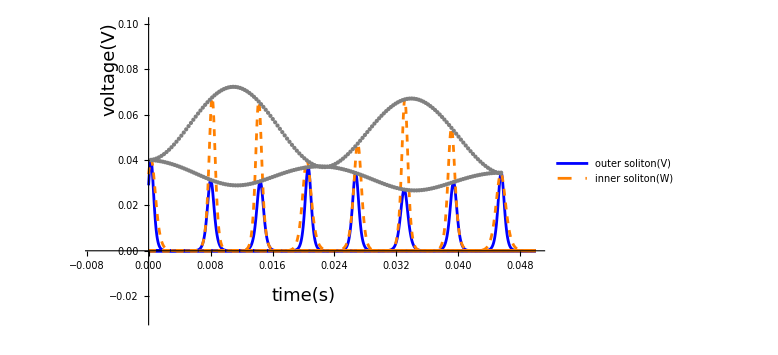

```mathematica
asymSolitonFun[asymSol2](*figure 4a in the article*)
```

## Velocity Plot

```mathematica
velocity[parameters_,t_]:=Module[
{k1,k2,te1,te2,deltheta1,vel},
k1=Evaluate[kk1[t/(24*α)]/.asymSol2];
k2=Evaluate[kk2[t/(24*α)]/.asymSol2];
te1=Evaluate[tte1[t/(24*α)]/.asymSol2];
te2=Evaluate[tte2[t/(24*α)]/.asymSol2];

deltheta1[parameters]:=4*k1^2+parameters[m1]-4/3*k1^2*parameters[f1]-1/k1^3/4*k2^3*NIntegrate[(Tanh[u]+Sech[u]^2*u)*(2*parameters[n2]/k2+4*parameters[m2]*Tanh[k2*u/k1+k2*(te1-te2)])*Sech[k2*u/k1+k2*(te1-te2)]^2,{u,-Infinity,Infinity}];

vel=β/α*(1+1/24*deltheta1[parameters]);
vel
]
```

```mathematica
velocity2[parameters_,t_]:=Module[
{k1,k2,te1,te2,deltheta2,vel2},
k1=Evaluate[kk1[t/(24*α)]/.asymSol2];
k2=Evaluate[kk2[t/(24*α)]/.asymSol2];
te1=Evaluate[tte1[t/(24*α)]/.asymSol2];
te2=Evaluate[tte2[t/(24*α)]/.asymSol2];

deltheta2[parameters]:=4*k2^2+parameters[m3]-4/3*k2^2*parameters[f2]-1/k2^3/4*k1^3*NIntegrate[(Tanh[u]+Sech[u]^2*u)*(2*parameters[n4]/k1+4*parameters[m4]*Tanh[k1*u/k2-k1*(te1-te2)])*Sech[k1*u/k2-k1*(te1-te2)]^2,{u,-Infinity,Infinity}];


vel2=β/α*(1+1/24*deltheta2[parameters]);
vel2
]
```

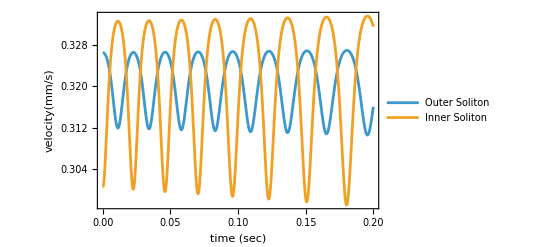

```mathematica
(*figure 5a in the article*)
Plot[{velocity[parameters2,x]*1000,velocity2[parameters2,x]*1000},{x,0,0.2},PlotRange->All,PlotLegends->{"Outer Soliton","Inner Soliton"},Frame->True,FrameStyle->Thick,FrameLabel->{"time (sec)","velocity(mm/s)"},LabelStyle->Directive[Bold,14]]
```

## Damping coefficient

```mathematica
oscillationData3=Table[Evaluate[kk1[x]/.asymSol2]-Evaluate[kk2[x]/.asymSol2],{x,0,500,0.01}];
flattenedData3=Flatten[oscillationData3];
peaks3=FindPeaks[flattenedData3];
xValues3=Table[x,{x,0,500,0.01}];
peakPoints3={xValues3[[#]],flattenedData3[[#]]}&/@peaks3[[All,1]];
fit3=FindFit[peakPoints3,A Exp[-k x],{{A,Max[peakPoints3[[All,2]]]},{k,0.01}},x];
kValue=k/. fit3
fittedFunction3[x_]:=A Exp[-k x]/. fit3;
```

0.00122975

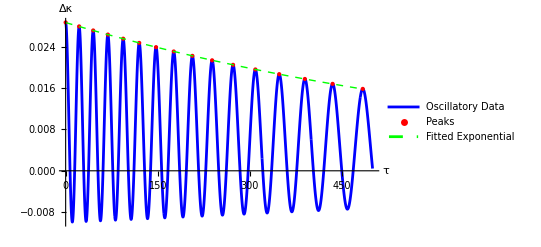

```mathematica
(*figure 7a in the article*)
Show[
ListLinePlot[Legended[Transpose[{xValues3,flattenedData3}],"Oscillatory Data"],PlotStyle->Blue],

ListPlot[Legended[peakPoints3,"Peaks"],PlotStyle->{Red,PointSize[Large]}],

Plot[Legended[fittedFunction3[x],"Fitted Exponential"],{x,Min[peakPoints3[[All,1]]],Max[peakPoints3[[All,1]]]},PlotStyle->{Green,Thick,Dashed}],

AxesLabel->{Style["τ",18],Style["Δκ",18]},AxesStyle->Thick,TicksStyle->Directive[14]
]
```

## FFT analysis and frequency calculation

```mathematica
dominantFreq[asymSol_,τmax_:500.,dτ_:0.01]:=Module[
{τ,xvals,x,dx,dt,fs,spec,freqs,amps,iMax},
(*1. Sample kk1-kk2*)
xvals=N@Range[0,τmax,dτ];
x=N@Table[Evaluate[kk1[τ]/. asymSol]-Evaluate[kk2[τ]/. asymSol],{τ,xvals}];
(*2. Differentiate numerically to remove offset/DC*)
dx=Differences[x]/dτ;
(*3. Sampling:physical dt and fs*)
dt=24. α dτ;
fs=1./dt;
(*4. FFT spectrum of derivative*)
spec=Abs[Fourier[dx]];
freqs=Range[0,fs-fs/Length[dx],fs/Length[dx]];
(*5. Positive half only*)
amps=spec[[1;;Floor[Length[spec]/2]]];
freqs=freqs[[1;;Length[amps]]];
(*6. Peak frequency*)
iMax=First@Ordering[amps,-1];
N[freqs[[iMax]]]]
```

```mathematica
dominantFreq[asymSol2]
```

39.078

## Analytical frequency

```mathematica
M2
```

1.33064

```mathematica
M4
```

2.0808

```mathematica
aa=8*kk+2/(45*kk)*(30+π^2)*(M2+M4)
```

72.9512

```mathematica
analyticFreq=1/((1/(Sqrt[(8*aa)/15*(M2+M4)*kk^3]/(2*π)))*24*α)(*Hz*)
```

43.3238

## Keeping the similar parameters as in analytical solution

```mathematica
parameters1c=<|m1->0,m2->M2,m3->0,m4->M4,n1->N1,n2->0,n3->N3,n4->0,ν1->0,ν2->0,f1->0,f2->0|>
```

<|m1→0,m2→1.33064,m3→0,m4→2.0808,n1→0.00130264,n2→0,n3→0.00238669,n4→0,ν1→0,ν2→0,f1→0,f2→0|>

```mathematica
asymSol1c=asymSolFun[parameters1c];
```

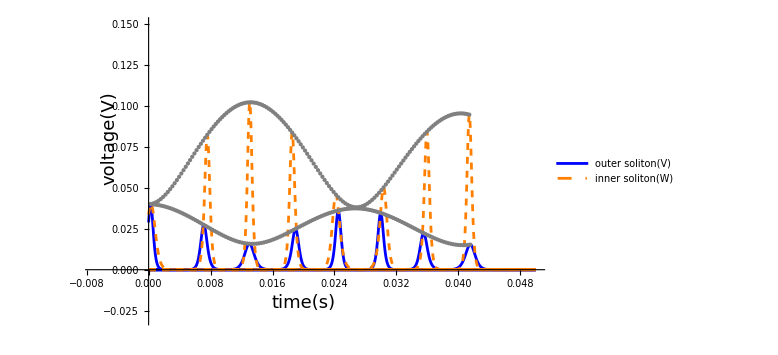

```mathematica
asymSolitonFun[asymSol1c,0.15](*figure 8a in the article*)
```

## Symmetric solution

```mathematica
parameters3=<|m1->M2,m2->M2,m3->M2,m4->M2,n1->N2,n2->N2,n3->N2,n4->N2,ν1->0,ν2->0,f1->F2,f2->F2|>
```

<|m1→1.33064,m2→1.33064,m3→1.33064,m4→1.33064,n1→0.00137516,n2→0.00137516,n3→0.00137516,n4→0.00137516,ν1→0,ν2→0,f1→-0.0441786,f2→-0.0441786|>

```mathematica
asymSol3=asymSolFun[parameters3];
```

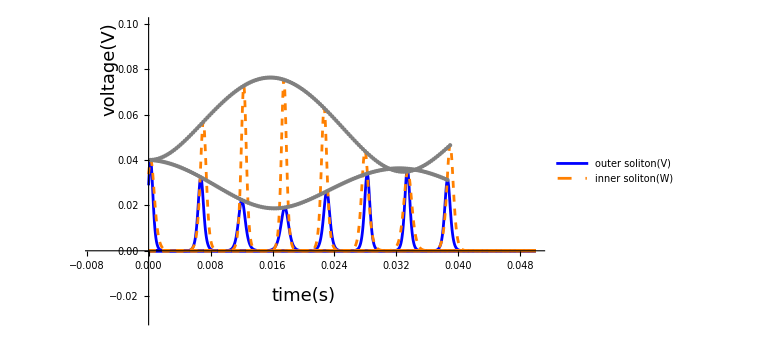

```mathematica
asymSolitonFun[asymSol3](*figure 9a in the article*)
```